```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["build/vals_rk-0.1_pa-50.0.dat.gz"];
```

```mathematica
rho = Exp[-6.0*data⟦2;;,1⟧]*data⟦2;;,3⟧;
```

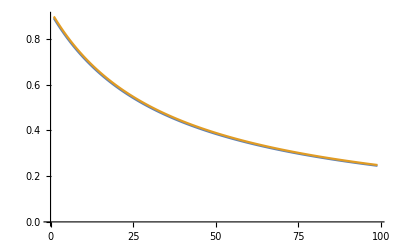

```mathematica
plots=ListPlot[{
-data⟦2;;,2⟧/3,
√(24π rho)/3
},PlotRange->All,Joined->True]
```

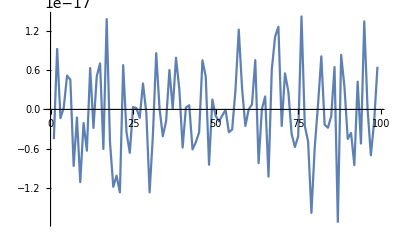

```mathematica
plots=ListPlot[{
data⟦2;;,4⟧
},PlotRange->All,Joined->True]
```